#### Specifying an unbiased coinfection model

As discussed at some length in Alizon (2013), care must be taken to construct a coinfection model that is unbiased. In particular, in models where there are only four host classes (susceptible, infected with the resident strain, infected with the mutant strain, and coinfected), invading mutants have a frequency-dependent advantage over the resident strain because the mutant can infect both susceptible hosts and hosts infected with the resident strain, but because the mutant is assumed to be coming in at very low density, there is no offsetting advantage for the resident strain because it can only infect susceptible hosts. As the abundance of the mutant increases, this fitness advantage disappears. 

The simplest way to eliminate this fitness advantage is to allow double infections - that is, hosts infected with the resident strain can become “doubly-infected” by coming in contact with already-infected hosts. Although it is possible to allow hosts to become doubly-infected with the mutant strain as well, this will be exceedingly rare during invasion, and thus will have no impact on whether or not the mutant strain can invade or not.  

We make the following assumptions, with an eye towards making the model as general as possible:
(i) We let the parameter σ determine the susceptibility of singly infected hosts to double- or co-infection. For simplicity, we assume that this parameter is the same across all strain combinations. If σ = 0, then we revert to a model without coinfection.
(ii) We assume that the shedding rate from double infections is the same as that from single infections. This assumption is because we assume that shedding rate scales with the total abundance of parasites within a host, which depends on the host body size. Thus, a doubly infected host has the same total abundance of parasites and the same shedding rate.
(iii) We assume that in coinfected hosts, on the other hand, the strains compete: the total abundance of parasites is still determined by host size, but a fraction x of that total is the resident strain, with the remaining (1-x) being the mutant strain. Thus if x=1, coinfected hosts will shed only the resident strain, whereas if x=0.5, the two strains equally divide the total abundance. 
(iv) We also assume that the mutant strain sheds at a lower rate than the resident strains, c λ, where 0≤ c≤1.

```mathematica
dS1dt=r1 (S1+I1r+D1rr+I1m+D1rm) (1-(S1+I1r+D1rr+I1m+D1rm)/K1)-β1 S1 (P1r+Pm);
dI1rdt=β1 S1 P1r-σ β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 (I1r+D1rr+x D1rm)-γ1 P1r;
dI1mdt=β1 S1 Pm-σ β1 I1m P1r-μ1 I1m;
dD1rmdt=σ β1 I1r Pm+σ β1 I1m P1r-μ1 D1rm;
dPmdt=c λ1 (I1m+(1-x) D1rm)-γ1 Pm;
```

Whether the mutant can invade can be determined by looking at the spectral radius of the next generation matrix:

```mathematica
Jac={{D[dS1dt,S1],D[dS1dt,I1r],D[dS1dt,D1rr],D[dS1dt,P1r],D[dS1dt,I1m],D[dS1dt,D1rm],D[dS1dt,Pm]},
{D[dI1dt,S1],D[dI1dt,I1r],D[dI1dt,D1rr],D[dI1dt,P1r],D[dI1dt,I1m],D[dI1dt,D1rm],D[dI1dt,Pm]},
{D[dD1rrdt,S1],D[dD1rrdt,I1r],D[dD1rrdt,D1rr],D[dD1rrdt,P1r],D[dD1rrdt,I1m],D[dD1rrdt,D1rm],D[dD1rrdt,Pm]},
{D[dP1rdt,S1],D[dP1rdt,I1r],D[dP1rdt,D1rr],D[dP1rdt,P1r],D[dP1rdt,I1m],D[dP1rdt,D1rm],D[dP1rdt,Pm]},
{D[dI1mdt,S1],D[dI1mdt,I1r],D[dI1mdt,D1rr],D[dI1mdt,P1r],D[dI1mdt,I1m],D[dI1mdt,D1rm],D[dI1mdt,Pm]},
{D[dD1rmdt,S1],D[dD1rmdt,I1r],D[dD1rmdt,D1rr],D[dD1rmdt,P1r],D[dD1rmdt,I1m],D[dD1rmdt,D1rm],D[dD1rmdt,Pm]},
{D[dPmdt,S1],D[dPmdt,I1r],D[dPmdt,D1rr],D[dPmdt,P1r],D[dPmdt,I1m],D[dPmdt,D1rm],D[dPmdt,Pm]}};
MatrixForm[Jmut=Jac[[5;;7,5;;7]]/.{I1m->0,D1rm->0,Pm->0}]
F={{0,0,β1 S1},{σ β1 P1r,0,σ β1 I1r},{0,0,0}};
V={{σ β1 P1r+μ1,0,0},{0,μ1,0},{-c λ1,-c λ1 (1-x),γ1}};
Jmut==F-V//Simplify
Inverse[V]
Eigenvalues[-V]
Dot[F,Inverse[V]]//MatrixForm
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

(-μ1-P1r β1 σ | 0 | S1 β1
P1r β1 σ | -μ1 | I1r β1 σ
c λ1 | c (1-x) λ1 | -γ1)

True

{{(γ1 μ1)/(γ1 μ1^2+P1r β1 γ1 μ1 σ),0,0},{0,(γ1 μ1+P1r β1 γ1 σ)/(γ1 μ1^2+P1r β1 γ1 μ1 σ),0},{(c λ1 μ1)/(γ1 μ1^2+P1r β1 γ1 μ1 σ),(c (1-x) λ1 (μ1+P1r β1 σ))/(γ1 μ1^2+P1r β1 γ1 μ1 σ),(μ1^2+P1r β1 μ1 σ)/(γ1 μ1^2+P1r β1 γ1 μ1 σ)}}

{-γ1,-μ1,-μ1-P1r β1 σ}

((c S1 β1 λ1 μ1)/(γ1 μ1^2+P1r β1 γ1 μ1 σ) | (c S1 (1-x) β1 λ1 (μ1+P1r β1 σ))/(γ1 μ1^2+P1r β1 γ1 μ1 σ) | (S1 β1 (μ1^2+P1r β1 μ1 σ))/(γ1 μ1^2+P1r β1 γ1 μ1 σ)
(P1r β1 γ1 μ1 σ)/(γ1 μ1^2+P1r β1 γ1 μ1 σ)+(c I1r β1 λ1 μ1 σ)/(γ1 μ1^2+P1r β1 γ1 μ1 σ) | (c I1r (1-x) β1 λ1 σ (μ1+P1r β1 σ))/(γ1 μ1^2+P1r β1 γ1 μ1 σ) | (I1r β1 σ (μ1^2+P1r β1 μ1 σ))/(γ1 μ1^2+P1r β1 γ1 μ1 σ)
0 | 0 | 0)

{0,-1/(2 γ1 μ1 (μ1+P1r β1 σ))β1 (-c S1 λ1 μ1-c I1r λ1 μ1 σ+c I1r x λ1 μ1 σ-c I1r P1r β1 λ1 σ^2+c I1r P1r x β1 λ1 σ^2+√(c λ1 (-4 P1r S1 (-1+x) γ1 μ1 σ (μ1+P1r β1 σ)+c λ1 (S1 μ1-I1r (-1+x) σ (μ1+P1r β1 σ))^2))),-1/(2 γ1 μ1 (μ1+P1r β1 σ))β1 (-c S1 λ1 μ1-c I1r λ1 μ1 σ+c I1r x λ1 μ1 σ-c I1r P1r β1 λ1 σ^2+c I1r P1r x β1 λ1 σ^2-√(c λ1 (-4 P1r S1 (-1+x) γ1 μ1 σ (μ1+P1r β1 σ)+c λ1 (S1 μ1-I1r (-1+x) σ (μ1+P1r β1 σ))^2)))}

The spectral radius must be larger than one for the mutant to be able to invade. The condition can be simplified somewhat:

```mathematica
-1/(2 γ1 μ1 (μ1+P1r β1 σ))β1 (-c S1 λ1 μ1-c I1r λ1 μ1 σ+c I1r x λ1 μ1 σ-c I1r P1r β1 λ1 σ^2+c I1r P1r x β1 λ1 σ^2-√(c λ1 (-4 P1r S1 (-1+x) γ1 μ1 σ (μ1+P1r β1 σ)+c λ1 (S1 μ1-I1r (-1+x) σ (μ1+P1r β1 σ))^2)))>1;
(-β1√(c λ1 (-4 P1r S1 (-1+x) γ1 μ1 σ (μ1+P1r β1 σ)+c λ1 (S1 μ1-I1r (-1+x) σ (μ1+P1r β1 σ))^2)))^2>(2 γ1 μ1 (σ P1r β1+μ1)+β1 (-c S1 λ1 μ1-c I1r λ1 μ1 σ+c I1r x λ1 μ1 σ-c I1r P1r β1 λ1 σ^2+c I1r P1r x β1 λ1 σ^2))^2//Simplify
```

γ1 μ1 (μ1+P1r β1 σ) (γ1 μ1 (μ1+P1r β1 σ)+c β1 λ1 (I1r (-1+x) σ (μ1+P1r β1 σ)-S1 (μ1-P1r (-1+x) β1 σ)))<0

Some further rearrangment leads to the following expression (which also must be greater than unity for the mutant to be able to invade):

```mathematica
γ1 μ1 (μ1+P1r β1 σ) (γ1 μ1 (μ1+P1r β1 σ)+c β1 λ1 (I1r (-1+x) σ (μ1+P1r β1 σ)-S1 (μ1-P1r (-1+x) β1 σ)))==γ1^2 μ1^2 (P1r β1 σ+μ1)^2-c β1 λ1 γ1 μ1 (P1r β1 σ+μ1)  (S1 (P1r (1-x) σ β1+μ1)+I1r (1-x) σ (P1r β1 σ+μ1))//Simplify
```

True

```mathematica
γ1 μ1 (P1r β1 σ+μ1) (γ1 μ1 (P1r β1 σ+μ1)+c β1 λ1 (I1r (-1+x) σ (μ1+P1r β1 σ)-S1 (μ1-P1r (-1+x) β1 σ)))<0;
γ1^2 μ1^2 (P1r β1 σ+μ1)^2-c β1 λ1 γ1 μ1 (P1r β1 σ+μ1)  (S1 (P1r (1-x) σ β1+μ1)+I1r (1-x) σ (P1r β1 σ+μ1))<0;
(c β1 λ1 γ1 μ1 (P1r β1 σ+μ1)  (S1 (P1r (1-x) σ β1+μ1)+I1r (1-x) σ (P1r β1 σ+μ1)))/(γ1^2 μ1^2 (P1r β1 σ+μ1)^2)>1;
```

Note that this expression is equivalent to the more biologically meaningful expression below. The first term is the probability that a spore in the environment encounters a host already infected with the resident strain. The second term is the expected amount of spores shed from a coinfected host. The third term is the probability a spore in the environment encounters a susceptible host. Once a host is singly infected with the mutant strain, there are two potential outcomes, captured by the terms in the parenthetical expression. The first term of the parenthetical is the probability that the singly infected host dies before becoming coinfected; the second term is the expected amount of shedding from a singly infected host. The third term of the parenthetical is the probability that the singly infected host will become coinfected; the fourth term is the expected amount of shedding from a coinfected host.

```mathematica
(c β1 λ1 γ1 μ1 (P1r β1 σ+μ1)  (S1 (P1r (1-x) σ β1+μ1)+I1r (1-x) σ (P1r β1 σ+μ1)))/(γ1^2 μ1^2 (P1r β1 σ+μ1)^2)==(σ β1 I1r)/γ1 (c λ1 (1-x))/μ1+(β1 S1)/γ1 (μ1/(σ β1 P1r+μ1) (c λ1)/μ1+(σ β1 P1r)/(σ β1 P1r+μ1) (c λ1 (1-x))/μ1)//Simplify
```

True

The condition for invasion is that the spectral radius is greater than one, which can be simplified to the following equation, which depends on the equilibrium of the resident-only model. The equilibria of the resident-only model (in terms of the equilibrium abundance of parasites in the environment) are:

```mathematica
P1rEq=Solve[(dI1rdt/.Pm->0/.D1rm->0)==0,P1r]
D1rrEq=Solve[(dP1rdt/.P1rEq[[1]]/.D1rm->0)==0,D1rr]
S1Eq=Solve[(dD1rrdt/.D1rrEq[[1]]/.P1rEq[[1]])==0,S1]
```

{{P1r→(I1r μ1)/(β1 (S1-I1r σ))}}

{{D1rr→-(I1r S1 β1 λ1-I1r γ1 μ1-I1r^2 β1 λ1 σ)/(β1 λ1 (S1-I1r σ))}}

{{S1→(γ1 μ1)/(β1 λ1)}}

The spectral radius, evaluated at the equilbrium, is the following:

```mathematica
(σ β1 I1r)/γ1 (c λ1 (1-x))/μ1+(β1 S1)/γ1 (μ1/(σ β1 P1r+μ1) (c λ1)/μ1+(σ β1 P1r)/(σ β1 P1r+μ1) (c λ1 (1-x))/μ1)/.P1rEq⟦1⟧/.S1Eq⟦1⟧//Simplify
```

(c (γ1 μ1+I1r (1-2 x) β1 λ1 σ))/(γ1 μ1)

Notice that if the resident and mutant are identical (x=0.5 and c=1) and coinfection is unbiased (σ=1), then the mutant is neutral (its fitness is equal to 1).

```mathematica
Simplify[(σ β1 I1r)/γ1 (c λ1 (1-x))/μ1+(β1 S1)/γ1 (μ1/(σ β1 P1r+μ1) (c λ1)/μ1+(σ β1 P1r)/(σ β1 P1r+μ1) (c λ1 (1-x))/μ1)/.P1rEq⟦1⟧/.S1Eq⟦1⟧/.c->1/.x->0.5/.σ->1]
```

1.

#### Specifying a two-host model with coinfection but without depletion of parasites from the environment

Now that I am confident in my ability to specify an unbiased coinfection model with a single host type, we can specify the coinfection model with two hosts and two specialist parasites, where the invading strain is a generalist.

```mathematica
dS1dt=r1 (S1+I1r+D1rr+I1m+D1rm) (1-(S1+I1r+D1rr+I1m+D1rm)/K1)-β1 S1 (P1r+Pm);
dI1rdt=β1 S1 P1r-σ1 β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ1 β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 (I1r+D1rr+x1 D1rm)-γ P1r;
dS2dt=r2 (S2+I2r+D2rr+I2m+D2rm) (1-(S2+I2r+D2rr+I2m+D2rm)/K2)-β2 S2 (P2r+Pm);
dI2rdt=β2 S2 P2r-σ2 β2 I2r (P2r+Pm)-μ2 I2r;
dD2rrdt=σ2 β2 I2r P2r-μ2 D2rr;
dP2rdt=λ2 (I2r+D2rr+x2 D2rm)-γ P2r;

dI1mdt=β1 S1 Pm-σ1 β1 I1m P1r-μ1 I1m;
dI2mdt=β2 S2 Pm-σ2 β2 I2m P2r-μ2 I2m;
dD1rmdt=σ1 β1 I1r Pm+σ1 β1 I1m P1r-μ1 D1rm;
dD2rmdt=σ2 β2 I2r Pm+σ2 β2 I2m P2r-μ2 D2rm;
dPmdt=c (λ1 I1m+λ2 I2m+(1-x1) λ1 D1rm+(1-x2) λ2 D2rm)-γ Pm;
```

Whether the mutant can invade will depend on the mutant Jacobian matrix:

```mathematica
MatrixForm[Jmut={{D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,D1rm],D[dI1mdt,D2rm],D[dI1mdt,Pm]},
{D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,D1rm],D[dI2mdt,D2rm],D[dI2mdt,Pm]},{D[dD1rmdt,I1m],D[dD1rmdt,I2m],D[dD1rmdt,D1rm],D[dD1rmdt,D2rm],D[dD1rmdt,Pm]},
{D[dD2rmdt,I1m],D[dD2rmdt,I2m],D[dD2rmdt,D1rm],D[dD2rmdt,D2rm],D[dD2rmdt,Pm]},
{D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,D1rm],D[dPmdt,D2rm],D[dPmdt,Pm]}}]
```

(-μ1-P1r β1 σ1 | 0 | 0 | 0 | S1 β1
0 | -μ2-P2r β2 σ2 | 0 | 0 | S2 β2
P1r β1 σ1 | 0 | -μ1 | 0 | I1r β1 σ1
0 | P2r β2 σ2 | 0 | -μ2 | I2r β2 σ2
c λ1 | c λ2 | c (1-x1) λ1 | c (1-x2) λ2 | -γ)

```mathematica
F={{0,0,0,0,Jmut[[1,5]]},
{0,0,0,0,Jmut[[2,5]]},
{Jmut[[3,1]],0,0,0,Jmut[[3,5]]},
{0,Jmut[[4,2]],0,0,Jmut[[4,5]]},
{0,0,0,0,0}};
V=F-Jmut;
(* Confirming that V meets the conditions to use the NGT *)
Inverse[V]
Eigenvalues[-V]
MatrixForm[Dot[F,Inverse[V]]]
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

{{(γ μ1 μ2^2+P2r β2 γ μ1 μ2 σ2)/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0,0},{0,(γ μ1^2 μ2+P1r β1 γ μ1 μ2 σ1)/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0},{0,0,1/μ1,0,0},{0,0,0,1/μ2,0},{(c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2)/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1)/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c (1-x1) λ1)/(γ μ1),(c (1-x2) λ2)/(γ μ2),1/γ}}

{-γ,-μ1,-μ2,-μ1-P1r β1 σ1,-μ2-P2r β2 σ2}

((S1 β1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (S1 β1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c S1 (1-x1) β1 λ1)/(γ μ1) | (c S1 (1-x2) β1 λ2)/(γ μ2) | (S1 β1)/γ
(S2 β2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (S2 β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c S2 (1-x1) β2 λ1)/(γ μ1) | (c S2 (1-x2) β2 λ2)/(γ μ2) | (S2 β2)/γ
(P1r β1 σ1 (γ μ1 μ2^2+P2r β2 γ μ1 μ2 σ2))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I1r β1 σ1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (I1r β1 σ1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I1r (1-x1) β1 λ1 σ1)/(γ μ1) | (c I1r (1-x2) β1 λ2 σ1)/(γ μ2) | (I1r β1 σ1)/γ
(I2r β2 σ2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (P2r β2 (γ μ1^2 μ2+P1r β1 γ μ1 μ2 σ1) σ2)/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I2r β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1) σ2)/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I2r (1-x1) β2 λ1 σ2)/(γ μ1) | (c I2r (1-x2) β2 λ2 σ2)/(γ μ2) | (I2r β2 σ2)/γ
0 | 0 | 0 | 0 | 0)

{0,0,0,(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (-4 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2+√(c (-4 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))}

The mutant can invade if the spectral radius is greater than one. The invasion condition can be reexpressed as:

```mathematica
(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (-4 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))>1;
(-√(c (-4 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))^2>((2 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))-(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2))^2//Simplify
```

γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)+c (-S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2-P2r (-1+x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (-μ1+P1r (-1+x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2))))<0

With some further manipulation, the invasion condition can be written as the following:

```mathematica
(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))^2-c γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)(S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2+P2r (1-x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (μ1+P1r (1-x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (1-x1) β1 λ1 μ2 σ1+I2r (1-x2) β2 λ2 μ1 σ2)))<0;
(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))^2-c γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)(S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2+P2r (1-x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (μ1+P1r (1-x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (1-x1) β1 λ1 μ2 σ1+I2r (1-x2) β2 λ2 μ1 σ2)))<0;
1/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))^2 (c γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)(S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2+P2r (1-x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (μ1+P1r (1-x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (1-x1) β1 λ1 μ2 σ1+I2r (1-x2) β2 λ2 μ1 σ2))))>1;
```

While this condition is essentially impossible to interpret in its current form, it has a biologically meaningful form:

```mathematica
1/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))^2 (c γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)(S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2+P2r (1-x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (μ1+P1r (1-x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (1-x1) β1 λ1 μ2 σ1+I2r (1-x2) β2 λ2 μ1 σ2))))==(σ1 β1 I1r)/γ (c λ1 (1-x1))/μ1+(β1 S1)/γ (μ1/(σ1 β1 P1r+μ1) (c λ1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1))/μ1)+(σ2 β2 I2r)/γ (c λ2 (1-x2))/μ2+(β2 S2)/γ (μ2/(σ2 β2 P2r+μ2) (c λ2)/μ2+(σ2 β2 P2r)/(σ2 β2 P2r+μ2) (c λ2 (1-x2))/μ2)//Simplify
Rm=(σ1 β1 I1r)/γ (c λ1 (1-x1))/μ1+(β1 S1)/γ (μ1/(σ1 β1 P1r+μ1) (c λ1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1))/μ1)+(σ2 β2 I2r)/γ (c λ2 (1-x2))/μ2+(β2 S2)/γ (μ2/(σ2 β2 P2r+μ2) (c λ2)/μ2+(σ2 β2 P2r)/(σ2 β2 P2r+μ2) (c λ2 (1-x2))/μ2);
```

True

```mathematica
P1rEq=Solve[(dI1rdt/.Pm->0/.D1rm->0)==0,P1r]
D1rrEq=Solve[(dP1rdt/.P1rEq[[1]]/.D1rm->0)==0,D1rr]
S1Eq=Solve[(dD1rrdt/.D1rrEq[[1]]/.P1rEq[[1]])==0,S1]
P2rEq=Solve[(dI2rdt/.Pm->0/.D2rm->0)==0,P2r]
D2rrEq=Solve[(dP2rdt/.P2rEq[[1]]/.D2rm->0)==0,D2rr]
S2Eq=Solve[(dD2rrdt/.D2rrEq[[1]]/.P2rEq[[1]])==0,S2]
```

{{P1r→(I1r μ1)/(β1 (S1-I1r σ1))}}

{{D1rr→-(I1r S1 β1 λ1-I1r γ μ1-I1r^2 β1 λ1 σ1)/(β1 λ1 (S1-I1r σ1))}}

{{S1→(γ μ1)/(β1 λ1)}}

{{P2r→(I2r μ2)/(β2 (S2-I2r σ2))}}

{{D2rr→-(I2r S2 β2 λ2-I2r γ μ2-I2r^2 β2 λ2 σ2)/(β2 λ2 (S2-I2r σ2))}}

{{S2→(γ μ2)/(β2 λ2)}}

Note that if there is no cost of generalism, the generalist should have a R_m=2 (because the mutant’s invasion fitness is equal to the sum of its invasion fitnesses on each host separately).

```mathematica
Rm/.P1rEq⟦1⟧/.P2rEq⟦1⟧/.S1Eq⟦1⟧/.S2Eq⟦1⟧/.{c->1,x1->0.5,x2->0.5,σ1->1,σ2->1}//FullSimplify
```

2.

If you disallow coinfection, you recover the results from the single-infection model. Without depletion of parasites from the environment, everything is very simple, and the cost is all that matters.

```mathematica
Rm/.{σ1->0,σ2->0}
Rm/.{σ1->0,σ2->0}/.{S1->(γ μ1)/(β1 λ1),S2->(γ μ2)/(β2 λ2)}
```

(c S1 β1 λ1)/(γ μ1)+(c S2 β2 λ2)/(γ μ2)

2 c

What if you allow coinfection and the two strains are equal competitors? Interestingly, you get the same result. All that matters is the cost of generalism.

```mathematica
Simplify[Rm/.P1rEq⟦1⟧/.P2rEq⟦1⟧/.S1Eq⟦1⟧/.S2Eq⟦1⟧/.{x1->0.5,x2->0.5}]
```

2. c

#### Specifying a two-host model with coinfection with depletion of parasites from the environment

Now that I am confident in my ability to specify an unbiased coinfection model with a single host type, we can specify the coinfection model with two hosts and two specialist parasites, where the invading strain is a generalist.

```mathematica
dS1dt=r1 (S1+I1r+D1rr+I1m+D1rm) (1-(S1+I1r+D1rr+I1m+D1rm)/K1)-β1 S1 (P1r+Pm);
dI1rdt=β1 S1 P1r-σ1 β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ1 β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 (I1r+D1rr+x1 D1rm)-β1 S1 P1r-σ1 β1 I1r P1r-σ1 β1 I1m P1r-γ P1r;
dS2dt=r2 (S2+I2r+D2rr+I2m+D2rm) (1-(S2+I2r+D2rr+I2m+D2rm)/K2)-β2 S2 (P2r+Pm);
dI2rdt=β2 S2 P2r-σ2 β2 I2r (P2r+Pm)-μ2 I2r;
dD2rrdt=σ2 β2 I2r P2r-μ2 D2rr;
dP2rdt=λ2 (I2r+D2rr+x2 D2rm)-β2 S2 P2r-σ2 β2 I2r P2r-σ2 β2 I2m P2r-γ P2r;

dI1mdt=β1 S1 Pm-σ1 β1 I1m P1r-μ1 I1m;
dI2mdt=β2 S2 Pm-σ2 β2 I2m P2r-μ2 I2m;
dD1rmdt=σ1 β1 I1r Pm+σ1 β1 I1m P1r-μ1 D1rm;
dD2rmdt=σ2 β2 I2r Pm+σ2 β2 I2m P2r-μ2 D2rm;
dPmdt=c (λ1 I1m+λ2 I2m+(1-x1) λ1 D1rm+(1-x2) λ2 D2rm)-β1 S1 Pm-β2 S2 Pm-σ1 β1 I1r Pm-σ2 β2 I2r Pm-γ Pm;
```

Whether the mutant can invade will depend on the mutant Jacobian matrix:

```mathematica
MatrixForm[Jmut={{D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,D1rm],D[dI1mdt,D2rm],D[dI1mdt,Pm]},
{D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,D1rm],D[dI2mdt,D2rm],D[dI2mdt,Pm]},{D[dD1rmdt,I1m],D[dD1rmdt,I2m],D[dD1rmdt,D1rm],D[dD1rmdt,D2rm],D[dD1rmdt,Pm]},
{D[dD2rmdt,I1m],D[dD2rmdt,I2m],D[dD2rmdt,D1rm],D[dD2rmdt,D2rm],D[dD2rmdt,Pm]},
{D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,D1rm],D[dPmdt,D2rm],D[dPmdt,Pm]}}]
```

(-μ1-P1r β1 σ1 | 0 | 0 | 0 | S1 β1
0 | -μ2-P2r β2 σ2 | 0 | 0 | S2 β2
P1r β1 σ1 | 0 | -μ1 | 0 | I1r β1 σ1
0 | P2r β2 σ2 | 0 | -μ2 | I2r β2 σ2
c λ1 | c λ2 | c (1-x1) λ1 | c (1-x2) λ2 | -S1 β1-S2 β2-γ-I1r β1 σ1-I2r β2 σ2)

```mathematica
F={{0,0,0,0,Jmut[[1,5]]},
{0,0,0,0,Jmut[[2,5]]},
{Jmut[[3,1]],0,0,0,Jmut[[3,5]]},
{0,Jmut[[4,2]],0,0,Jmut[[4,5]]},
{0,0,0,0,0}};
V=F-Jmut;
(* Confirming that V meets the conditions to use the NGT *)
Inverse[V]
Eigenvalues[-V]
MatrixForm[Dot[F,Inverse[V]]]
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

{{(μ1 μ2^2+P2r β2 μ1 μ2 σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0,0},{0,(μ1^2 μ2+P1r β1 μ1 μ2 σ1)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0},{0,0,1/μ1,0,0},{0,0,0,1/μ2,0},{(c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)),(c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1)/(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)),(c (1-x1) λ1)/(μ1 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)),(c (1-x2) λ2)/(μ2 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)),1/(S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)}}

{-μ1,-μ2,-μ1-P1r β1 σ1,-S1 β1-S2 β2-γ-I1r β1 σ1-I2r β2 σ2,-μ2-P2r β2 σ2}

((S1 β1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)) | (S1 β1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)) | (c S1 (1-x1) β1 λ1)/(μ1 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)) | (c S1 (1-x2) β1 λ2)/(μ2 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)) | (S1 β1)/(S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)
(S2 β2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)) | (S2 β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)) | (c S2 (1-x1) β2 λ1)/(μ1 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)) | (c S2 (1-x2) β2 λ2)/(μ2 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)) | (S2 β2)/(S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)
(P1r β1 σ1 (μ1 μ2^2+P2r β2 μ1 μ2 σ2))/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I1r β1 σ1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)) | (I1r β1 σ1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)) | (c I1r (1-x1) β1 λ1 σ1)/(μ1 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)) | (c I1r (1-x2) β1 λ2 σ1)/(μ2 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)) | (I1r β1 σ1)/(S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)
(I2r β2 σ2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)) | (P2r β2 (μ1^2 μ2+P1r β1 μ1 μ2 σ1) σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I2r β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1) σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)) | (c I2r (1-x1) β2 λ1 σ2)/(μ1 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)) | (c I2r (1-x2) β2 λ2 σ2)/(μ2 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)) | (I2r β2 σ2)/(S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)
0 | 0 | 0 | 0 | 0)

{0,0,0,(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (-4 μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)),(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2+√(c (-4 μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2))}

The mutant can invade if the spectral radius is greater than one. The invasion condition can be reexpressed as:

```mathematica
(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (-4 μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2))>1;
(-√(c (-4 μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))^2>((2 μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2))-(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2))^2//Simplify
```

μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2) (μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)+c (-S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2-P2r (-1+x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (-μ1+P1r (-1+x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2))))<0

With some further manipulation, the invasion condition can be written as the following:

```mathematica
μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2) (μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)+c (-S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2-P2r (-1+x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (-μ1+P1r (-1+x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2))))==(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2))^2-(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)) (c (S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2+P2r (1-x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (μ1+P1r (1-x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (1-x1) β1 λ1 μ2 σ1+I2r (1-x2) β2 λ2 μ1 σ2))))//Simplify
(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2))^2-(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)) (c (S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2+P2r (1-x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (μ1+P1r (1-x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (1-x1) β1 λ1 μ2 σ1+I2r (1-x2) β2 λ2 μ1 σ2))))<0;
1/(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2))^2(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)) (c (S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2+P2r (1-x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (μ1+P1r (1-x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (1-x1) β1 λ1 μ2 σ1+I2r (1-x2) β2 λ2 μ1 σ2))))>1;
```

True

While this condition is essentially impossible to interpret in its current form, it has a biologically meaningful form:

```mathematica
1/(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2))^2(μ1 μ2 (μ1+P1r β1 σ1) (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2) (μ2+P2r β2 σ2)) (c (S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2+P2r (1-x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (μ1+P1r (1-x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (1-x1) β1 λ1 μ2 σ1+I2r (1-x2) β2 λ2 μ1 σ2))))==(σ1 β1 I1r)/(S1 β1+S2 β2+I1r β1 σ1+I2r β2 σ2+γ) (c λ1 (1-x1))/μ1+(β1 S1)/(S1 β1+S2 β2+I1r β1 σ1+I2r β2 σ2+γ) (μ1/(σ1 β1 P1r+μ1) (c λ1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1))/μ1)+(σ2 β2 I2r)/(S1 β1+S2 β2+I1r β1 σ1+I2r β2 σ2+γ) (c λ2 (1-x2))/μ2+(β2 S2)/(S1 β1+S2 β2+I1r β1 σ1+I2r β2 σ2+γ) (μ2/(σ2 β2 P2r+μ2) (c λ2)/μ2+(σ2 β2 P2r)/(σ2 β2 P2r+μ2) (c λ2 (1-x2))/μ2)//Simplify
Rm=(σ1 β1 I1r)/(S1 β1+S2 β2+I1r β1 σ1+I2r β2 σ2+γ) (c λ1 (1-x1))/μ1+(β1 S1)/(S1 β1+S2 β2+I1r β1 σ1+I2r β2 σ2+γ) (μ1/(σ1 β1 P1r+μ1) (c λ1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1))/μ1)+(σ2 β2 I2r)/(S1 β1+S2 β2+I1r β1 σ1+I2r β2 σ2+γ) (c λ2 (1-x2))/μ2+(β2 S2)/(S1 β1+S2 β2+I1r β1 σ1+I2r β2 σ2+γ) (μ2/(σ2 β2 P2r+μ2) (c λ2)/μ2+(σ2 β2 P2r)/(σ2 β2 P2r+μ2) (c λ2 (1-x2))/μ2);
```

True

```mathematica
P1rEq=Solve[(dI1rdt/.Pm->0/.D1rm->0)==0,P1r];
D1rrEq=Solve[(dP1rdt/.P1rEq[[1]]/.D1rm->0/.I1m->0)==0,D1rr];
S1Eq=Solve[(dD1rrdt/.D1rrEq[[1]]/.P1rEq[[1]])==0,S1]
P1rEq=Simplify[P1rEq/.S1Eq[[1]]]
D1rrEq=Simplify[D1rrEq/.S1Eq[[1]]];
I1rEq=Solve[Simplify[dS1dt/.{D1rm->0,I1m->0,Pm->0}/.D1rrEq[[1]]/.S1Eq[[1]]/.P1rEq[[1]]]==0,I1r];
P2rEq=Solve[(dI2rdt/.Pm->0/.D2rm->0)==0,P2r];
D2rrEq=Solve[(dP2rdt/.P2rEq[[1]]/.D2rm->0/.I2m->0)==0,D2rr];
S2Eq=Solve[(dD2rrdt/.D2rrEq[[1]]/.P2rEq[[1]])==0,S2]
P2rEq=Simplify[P2rEq/.S2Eq[[1]]]
D2rrEq=Simplify[D2rrEq/.S2Eq[[1]]];
I2rEq=Solve[Simplify[dS2dt/.{D2rm->0,I2m->0,Pm->0}/.D2rrEq[[1]]/.S2Eq[[1]]/.P2rEq[[1]]]==0,I2r];
```

{{S1→-(μ1 (γ+I1r β1 σ1))/(β1 (-λ1+μ1))}}

{{P1r→-(I1r μ1 (-λ1+μ1))/(γ μ1-I1r β1 (λ1-2 μ1) σ1)}}

{{S2→-(μ2 (γ+I2r β2 σ2))/(β2 (-λ2+μ2))}}

{{P2r→-(I2r μ2 (-λ2+μ2))/(γ μ2-I2r β2 (λ2-2 μ2) σ2)}}

Note that for OverHat[S_1] and OverHat[P_(1r)] to be positive, the following must be true: λ_1-μ_1>0 and σ_1 β_1 OverHat[I_(1r)] (λ_1-2 μ_1)-γ μ_1<0.

The mutant invasion exponent evaluated at the equilibrium can be simplified to the following expression:

```mathematica
(Simplify[Rm/.S1Eq[[1]]/.P1rEq[[1]]/.S2Eq[[1]]/.P2rEq[[1]]]/.{x1->1/2,x2->1/2})==(-c (γ μ1 μ2 (λ2 μ1-λ1 (2 λ2-μ2))-I1r β1 λ1 μ1 (λ2-μ2) μ2 σ1-I2r β2 λ2 (λ1-μ1) μ1 μ2 σ2))/(μ1 μ2 (γ (λ1 λ2-μ1 μ2)+I1r β1 λ1 (λ2-μ2) σ1+I2r β2 λ2 (λ1-μ1) σ2))//Simplify
```

True

The derivative of the invasion exponent with respect to W can be simplified to the following expression. The denominator must be positive, so since we are only interested in the sign of the expression, we can focus only the numerator:

```mathematica
dRmdW=Simplify[D[Rm/.S1Eq[[1]]/.P1rEq[[1]]/.S2Eq[[1]]/.P2rEq[[1]]/.{x1->1/2,x2->1/2,σ1->1,σ2->1}/.{λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],I1r->I1r[W],I2r->I2r[W]},W]/.{μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W)}]
```

(c γ (λ2[W] μ1[W]^2 (-W β2 λ2[W] I2r'[W]+μ2[W] (γ+β2 I2r[W]+W β2 I2r'[W]))+λ1[W]^2 (-W β1 μ2[W]^2 I1r'[W]-W λ2[W]^2 (β1 I1r'[W]+β2 I2r'[W])+λ2[W] μ2[W] (γ+β2 I2r[W]+2 W β1 I1r'[W]+W β2 I2r'[W]))+λ1[W] μ1[W] (μ2[W]^2 (γ+β1 I1r[W]+W β1 I1r'[W])-2 λ2[W] μ2[W] (2 γ+β1 I1r[W]+β2 I2r[W]+W β1 I1r'[W]+W β2 I2r'[W])+λ2[W]^2 (γ+β1 I1r[W]+W β1 I1r'[W]+2 W β2 I2r'[W]))))/(W (μ1[W] (β2 I2r[W] λ2[W]+γ μ2[W])-λ1[W] ((γ+β1 I1r[W]+β2 I2r[W]) λ2[W]-β1 I1r[W] μ2[W]))^2)

This numerator can be simplified to the following expression. Note that every parenthetical term is positive, so if increasing host body size decreases the equilibrium abundance of singly infected hosts (i.e., OverHat[I_(1r)]'(W)<0 and OverHat[I_(2r)]'(W)<0), then increasing host body size is guaranteed to increase R_m.

```mathematica
Collect[Expand[Numerator[dRmdW]],{I1r[W],I2r[W],I1r'[W],I2r'[W]}]==c γ^2 (λ2[W]μ2[W] (λ1[W]-μ1[W])^2+λ1[W] μ1[W] (λ2[W]-μ2[W])^2)+I2r[W] c β2 γ λ2[W] (λ1[W]-μ1[W])^2 μ2[W]+I1r[W] c β1 γ λ1[W] μ1[W] (λ2[W]-μ2[W])^2-I1r'[W] c W β1 γ λ1[W] (λ1[W]-μ1[W]) (λ2[W]-μ2[W])^2-I2r'[W]c W β2 γ λ2[W] (λ1[W]-μ1[W])^2 (λ2[W]-μ2[W])//Simplify
```

True

However, if OverHat[I_(1r)]'(W)>0, then increasing host size must also increase the equilibrium abundance of susceptible hosts (i.e., OverHat[S_1]'(W)>0):

```mathematica
Simplify[D[S1Eq[[1,1,2]]/.{r1->r1[W],λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],K1->K1[W],I1r->I1r[W]},W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),K1'[W]->(-3 K1[W])/(4 W),r1'[W]->(-r1[W])/(4 W)}]==-(μ1[W] (γ λ1[W]+β1 σ1 I1r[W] λ1[W]- β1 σ1 W (λ1[W]-μ1[W]) I1r'[W]))/(W β1 (λ1[W]-μ1[W])^2)//Simplify
```

True

However, because increasing W decreases both maximum per-capita growth rate (r) and carrying capacity (K), and increases the shedding of parasites from infected hosts, the number of susceptible hosts at equilibrium would seem more likely to be a decreasing function of host body size (i.e., OverHat[S_1]'(W)<0), as the overall rate of increase is reduced but there may be more transmission events. For the model without coinfection, it is easy to prove that OverHat[S_1]'(W)<0. This strongly suggests that OverHat[S_1]'(W)<0, which can only be the case if OverHat[I_(1r)]'(W)>0. Notice that OverHat[I_(1r)]'(W)>0 also implies that increasing host body size increases the equilibrium abundance of parasites in the environment (i.e., OverHat[P_(1r)]'(W)>0; this is true of the model without coinfection as well):

```mathematica
(D[P1rEq[[1,1,2]]/.{r1->r1[W],λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],K1->K1[W],I1r->I1r[W]},W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),K1'[W]->(-3 K1[W])/(4 W),r1'[W]->(-r1[W])/(4 W)})//Simplify
```

(μ1[W] (γ I1r[W] μ1[W] (3 λ1[W]+μ1[W])+β1 σ1 I1r[W]^2 (λ1[W]^2+λ1[W] μ1[W]+2 μ1[W]^2)+4 W γ (λ1[W]-μ1[W]) μ1[W] I1r'[W]))/(4 W (β1 σ1 I1r[W] (λ1[W]-2 μ1[W])-γ μ1[W])^2)

Thus we can safely conclude that OverHat[I_(1r)]'(W)>0, making it impossible to a priori determine whether R_m'(W) is positive or negative.

To investigate further requires numerical analysis.

Allen et al. 2002 gives the allometric relationship between carrying capacity in individuals per km^2 and weight in grams, assuming that E = 0.78.
Savage et al. 2004 gives the allometric relationships between mortality rate (1/yr) and mass in grams, and between growth rate (1/yr) and weight in grams.
The growth rate data suggested a value of E=0.35, but Gillooly et al. 2001 suggested a value of E=0.43 for fish.

These differences are very non-trivial. For example, Allen et al. 2002 shows some data where log(K e^(-E/k T))=-20. If E=0.43, this value suggests a carrying capacity of 0.02 individuals/km^2, whereas a value of E=.78 yields 9800 individuals/km^2.

```mathematica
Solve[Log[K Exp[-Ε/(k T)]]==-20,K]/.{Ε->0.43,k->8.62/10^5,T->310}
Solve[Log[K Exp[-Ε/(k T)]]==-20,K]/.{Ε->0.78,k->8.62/10^5,T->310}
```

{{K→0.0200728}}

{{K→9793.09}}

Thus I will allow E to be different for the two functions.

```mathematica
allom={K1->K0 Exp[0.78/(k T)] W^(-3/4),K2->K0 Exp[0.78/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-0.43/(k T)] W^(-1/4),μ2->μ0 Exp[-0.43/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-0.43/(k T)] W^(3/4),λ2->λ0 Exp[-0.43/(k T)] (f W)^(3/4),r1->r0 Exp[-0.43/(k T)] W^(-1/4),r2->r0 Exp[-0.43/(k T)] (f W)^(-1/4)};
allompars={k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

```mathematica
S1allom=S1Eq[[1]]/.I1rEq[[2]]/.allom/.allompars;
S2allom=S2Eq[[1]]/.I2rEq[[2]]/.allom/.allompars;
P1allom=P1rEq[[1]]/.I1rEq[[2]]/.allom/.allompars;
P2allom=P2rEq[[1]]/.I2rEq[[2]]/.allom/.allompars;
I1allom=I1rEq[[2]]/.allom/.allompars;
I2allom=I2rEq[[2]]/.allom/.allompars;
Rmallom=Rm/.S1allom/.S2allom/.P1allom/.P2allom/.I1allom/.I2allom/.allom/.allompars;
```

```mathematica
pars={β1->1,β2->1,γ->0.1,σ2->1,W->20,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2};
sol=NDSolve[{S1'[t]==(dS1dt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
I1r'[t]==(dI1rdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
D1rr'[t]==(dD1rrdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
P1r'[t]==(dP1rdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
S1[0]==100,
I1r[0]==1,
D1rr[0]==1,
P1r[0]==1},{S1,I1r,D1rr,P1r},{t,0,100}]
I1r[100]/.sol
I1rEq/.allom/.allompars/.pars
```

{{S1→InterpolatingFunction[{{0., 100.}}, <>],I1r→InterpolatingFunction[{{0., 100.}}, <>],D1rr→InterpolatingFunction[{{0., 100.}}, <>],P1r→InterpolatingFunction[{{0., 100.}}, <>]}}

{0.00490005}

{{I1r→-0.1},{I1r→28.1566-0.000102108 ⅈ},{I1r→-4.13917×10^7-9.31323×10^-10 ⅈ},{I1r→-28.2726+0.00010211 ⅈ}}

```mathematica
pars={β1->10,β2->10,γ->0.1,σ2->1,W->50,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2};
allom/.allompars/.pars
pars={β1->10,β2->10,γ->0.1,σ2->1,W->500,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2};
allom/.allompars/.pars
```

{K1→0.039859,K2→0.0431365,μ1→0.267264,μ2→0.274397,λ1→14.9728,λ2→13.8352,r1→33.0898,r2→33.973}

{K1→0.00708805,K2→0.00767087,μ1→0.150294,μ2→0.154305,λ1→84.1981,λ2→77.8008,r1→18.6078,r2→19.1044}

```mathematica
(* Log[r M^(1/4)]=-0.68/(k T)+25.98 *)
(* r M^(1/4)=Exp[-0.68/kT] Exp[25.98] *)
```

```mathematica
{Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10}
```

```mathematica
(* Log[K Exp[-E/kT]] = -3/4 Log[M]-19.63 *)
(* Log[K Exp[-E/kT]] = Log[M^(-3/4)]-19.63 *)
(* K Exp[-E/kT] = Exp[-19.63] M^(-3/4) *)
(* K = 2.9/10^9 Exp[E/kT] M^(-3/4) *)
```

```mathematica
Solve[Log[K Exp[-Ε/(k T)]]==-20,K]/.{Ε->0.78,k->8.62/10^5,T->310}
```

{{K→9793.09}}

```mathematica
Exp[-19.63]//N
```

2.984×10^-9

```mathematica
pars={β1->10,β2->10,γ->0.1,σ2->1,W->50,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2};
sol=NDSolve[{S1'[t]==(dS1dt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
I1r'[t]==(dI1rdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
D1rr'[t]==(dD1rrdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
P1r'[t]==(dP1rdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
S1[0]==100,
I1r[0]==1,
D1rr[0]==1,
P1r[0]==1},{S1,I1r,D1rr,P1r},{t,0,1000}]
S1[1000]/.sol
I1r[1000]/.sol
S1Eq/.allom/.allompars/.pars
I1rEq/.allom/.allompars/.pars
```

{{S1→InterpolatingFunction[{{0., 1000.}}, <>],I1r→InterpolatingFunction[{{0., 1000.}}, <>],D1rr→InterpolatingFunction[{{0., 1000.}}, <>],P1r→InterpolatingFunction[{{0., 1000.}}, <>]}}

{0.000185092}

{0.000184226}

{{S1→0.00181744 (0.1+10 I1r)}}

{{I1r→-0.01},{I1r→0.000175924-2.88606×10^-9 ⅈ},{I1r→-65.8375-7.94032×10^-13 ⅈ},{I1r→-0.0179911+2.88686×10^-9 ⅈ}}

{0.00458136}

{S1→0.00488494-3.93713×10^-12 ⅈ}

{{I1r→-0.1},{I1r→0.00458154-8.42899×10^-11 ⅈ},{I1r→-28.8219-3.67706×10^-13 ⅈ},{I1r→-0.12091+8.46576×10^-11 ⅈ}}

```mathematica
I2allom/.{β1->1,β2->1,γ->0.1,σ2->1,W->200,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2}
P2allom/.{β1->1,β2->1,γ->0.1,σ2->1,W->200,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2}
S2allom/.{β1->1,β2->1,γ->0.1,σ2->1,W->200,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2}
I2allom/.{β1->1,β2->1,γ->0.1,σ2->1,W->200,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2}
P2allom/.{β1->1,β2->1,γ->0.1,σ2->1,W->200,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2}
```

{S2→1.88899+3.45768×10^-20 ⅈ}

{I2r→378.985+6.93889×10^-18 ⅈ}

{P2r→-0.195+4.71788×10^-27 ⅈ}

{S2→1.88899+3.45768×10^-20 ⅈ}

{I2r→378.985+6.93889×10^-18 ⅈ}

{P2r→-0.195+4.71788×10^-27 ⅈ}

```mathematica
(Rmallom/.{β1->1,β2->1,γ->0.1,σ2->1,W->300,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2})
```

0.800023+2.20873×10^-25 ⅈ

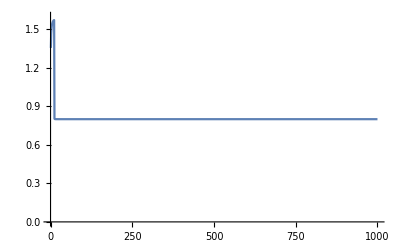

```mathematica
ListLinePlot[Re[RmW]]
```

```mathematica
RmW=Table[(Rmallom/.{β1->1,β2->1,γ->0.1,σ2->1,W->Wv,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2}),{Wv,10,10000,10}];
```

```mathematica
{{D[dS1dt/.{D1rm->0,I1m->0,Pm->0},S1],D[dS1dt/.{D1rm->0,I1m->0,Pm->0},I1r],D[dS1dt/.{D1rm->0,I1m->0,Pm->0},D1rr],D[dS1dt/.{D1rm->0,I1m->0,Pm->0},P1r]},
{D[dI1rdt/.{D1rm->0,I1m->0,Pm->0},S1],D[dI1rdt/.{D1rm->0,I1m->0,Pm->0},I1r],D[dI1rdt/.{D1rm->0,I1m->0,Pm->0},D1rr],D[dI1rdt/.{D1rm->0,I1m->0,Pm->0},P1r]},
{D[dD1rrdt/.{D1rm->0,I1m->0,Pm->0},S1],D[dD1rrdt/.{D1rm->0,I1m->0,Pm->0},I1r],D[dD1rrdt/.{D1rm->0,I1m->0,Pm->0},D1rr],D[dD1rrdt/.{D1rm->0,I1m->0,Pm->0},P1r]},
{D[dP1rdt/.{D1rm->0,I1m->0,Pm->0},S1],D[dP1rdt/.{D1rm->0,I1m->0,Pm->0},I1r],D[dP1rdt/.{D1rm->0,I1m->0,Pm->0},D1rr],D[dP1rdt/.{D1rm->0,I1m->0,Pm->0},P1r]}}/.{S1->K1,I1r->0,D1rr->0,P1r->0}//Eigenvalues
```

{-r1,-μ1,1/2 (-K1 β1-γ-μ1-√((K1 β1+γ+μ1)^2-4 (-K1 β1 λ1+K1 β1 μ1+γ μ1))),1/2 (-K1 β1-γ-μ1+√((K1 β1+γ+μ1)^2-4 (-K1 β1 λ1+K1 β1 μ1+γ μ1)))}

```mathematica
1/2 (-K1 β1-γ-μ1+√((K1 β1+γ+μ1)^2-4 (-K1 β1 λ1+K1 β1 μ1+γ μ1)))>0;
Simplify[(√((K1 β1+γ+μ1)^2-4 (-K1 β1 λ1+K1 β1 μ1+γ μ1)))^2>(K1 β1+γ+μ1)^2]
Simplify[D[(K1[W] β1 (λ1[W]-μ1[W]))/(γ μ1[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),K1'[W]->(-3 K1[W])/(4 W)}]
```

K1 β1 (λ1-μ1)>γ μ1

(β1 K1[W] (λ1[W]+3 μ1[W]))/(4 W γ μ1[W])

#### GARBAGE BELOW HERE!!

```mathematica
Simplify[D[D1rrEq[[1,1,2]]/.{r1->r1[W],λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],K1->K1[W],I1r->I1r[W]},W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),K1'[W]->(-3 K1[W])/(4 W),r1'[W]->(-r1[W])/(4 W)}]==(β1 σ1 I1r[W] (γ I1r[W] λ1[W] μ1[W]+β1 σ1 I1r[W]^2 λ1[W] μ1[W]-W (λ1[W]-μ1[W]) (β1 σ1 I1r[W] (λ1[W]-2 μ1[W])-2 γ μ1[W])I1r'[W]))/(W (β1 σ1 I1r[W] (λ1[W]-2 μ1[W])-γ μ1[W])^2)//Simplify
```

True

```mathematica
Solve[Simplify[D[(dS1dt+dI1rdt+dD1rrdt/.{D1rm->0,I1m->0,Pm->0}/.S1Eq[[1]]/.D1rrEq[[1]]/.{r1->r1[W],λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],K1->K1[W],I1r->I1r[W]}),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),K1'[W]->(-3 K1[W])/(4 W),r1'[W]->(-r1[W])/(4 W)}/.r1[W]->(I1r[W] μ1[W]-(β1 σ1 I1r[W]^2 (λ1[W]-μ1[W]) μ1[W])/(β1 σ1 I1r[W] (λ1[W]-2 μ1[W])-γ μ1[W]))/((I1r[W]-((γ+β1 σ1 I1r[W]) μ1[W])/(β1 (-λ1[W]+μ1[W]))-(β1 σ1 I1r[W]^2 (λ1[W]-μ1[W]))/(β1 σ1 I1r[W] (λ1[W]-2 μ1[W])-γ μ1[W])) (1-(I1r[W]-((γ+β1 σ1 I1r[W]) μ1[W])/(β1 (-λ1[W]+μ1[W]))-(β1 σ1 I1r[W]^2 (λ1[W]-μ1[W]))/(β1 σ1 I1r[W] (λ1[W]-2 μ1[W])-γ μ1[W]))/K1[W]))/.{σ1->1,σ2->1,x1->1/2,x2->1/2}]==0,I1r'[W]]//Simplify
```

{{I1r'[W]→(I1r[W] (γ+β1 I1r[W]) (β1^3 I1r[W]^3 μ1[W]^2 (-9 λ1[W]^2+11 λ1[W] μ1[W]+6 μ1[W]^2)+γ^2 μ1[W]^2 (4 β1 K1[W] λ1[W] (-λ1[W]+μ1[W])+γ μ1[W] (5 λ1[W]+3 μ1[W]))+β1 γ I1r[W] μ1[W] (8 β1 K1[W] λ1[W] (λ1[W]^2-3 λ1[W] μ1[W]+2 μ1[W]^2)+3 γ μ1[W] (-3 λ1[W]^2+7 λ1[W] μ1[W]+4 μ1[W]^2))+β1^2 I1r[W]^2 (-4 β1 K1[W] λ1[W] (λ1[W]-2 μ1[W])^2 (λ1[W]-μ1[W])+3 γ μ1[W]^2 (-6 λ1[W]^2+9 λ1[W] μ1[W]+5 μ1[W]^2))))/(4 W (λ1[W]-μ1[W]) (2 β1^3 γ I1r[W]^3 μ1[W]^3+β1^4 I1r[W]^4 μ1[W]^2 (-λ1[W]+2 μ1[W])-2 β1 γ^2 I1r[W] (λ1[W]-2 μ1[W]) μ1[W] (β1 K1[W] (λ1[W]-μ1[W])-γ μ1[W])+β1^2 γ I1r[W]^2 (λ1[W]-μ1[W]) (β1 K1[W] (λ1[W]-2 μ1[W])^2+3 γ μ1[W]^2)-γ^3 μ1[W]^2 (γ μ1[W]+β1 K1[W] (-λ1[W]+μ1[W]))))}}

```mathematica
Expand[(β1^3 I1r[W]^3 μ1[W]^2 (-9 λ1[W]^2+11 λ1[W] μ1[W]+6 μ1[W]^2)+γ^2 μ1[W]^2 (4 β1 K1[W] λ1[W] (-λ1[W]+μ1[W])+γ μ1[W] (5 λ1[W]+3 μ1[W]))+β1 γ I1r[W] μ1[W] (8 β1 K1[W] λ1[W] (λ1[W]^2-3 λ1[W] μ1[W]+2 μ1[W]^2)+3 γ μ1[W] (-3 λ1[W]^2+7 λ1[W] μ1[W]+4 μ1[W]^2))+β1^2 I1r[W]^2 (-4 β1 K1[W] λ1[W] (λ1[W]-2 μ1[W])^2 (λ1[W]-μ1[W])+3 γ μ1[W]^2 (-6 λ1[W]^2+9 λ1[W] μ1[W]+5 μ1[W]^2)))]
```

-4 β1^3 I1r[W]^2 K1[W] λ1[W]^4+8 β1^2 γ I1r[W] K1[W] λ1[W]^3 μ1[W]+20 β1^3 I1r[W]^2 K1[W] λ1[W]^3 μ1[W]-9 β1 γ^2 I1r[W] λ1[W]^2 μ1[W]^2-18 β1^2 γ I1r[W]^2 λ1[W]^2 μ1[W]^2-9 β1^3 I1r[W]^3 λ1[W]^2 μ1[W]^2-4 β1 γ^2 K1[W] λ1[W]^2 μ1[W]^2-24 β1^2 γ I1r[W] K1[W] λ1[W]^2 μ1[W]^2-32 β1^3 I1r[W]^2 K1[W] λ1[W]^2 μ1[W]^2+5 γ^3 λ1[W] μ1[W]^3+21 β1 γ^2 I1r[W] λ1[W] μ1[W]^3+27 β1^2 γ I1r[W]^2 λ1[W] μ1[W]^3+11 β1^3 I1r[W]^3 λ1[W] μ1[W]^3+4 β1 γ^2 K1[W] λ1[W] μ1[W]^3+16 β1^2 γ I1r[W] K1[W] λ1[W] μ1[W]^3+16 β1^3 I1r[W]^2 K1[W] λ1[W] μ1[W]^3+3 γ^3 μ1[W]^4+12 β1 γ^2 I1r[W] μ1[W]^4+15 β1^2 γ I1r[W]^2 μ1[W]^4+6 β1^3 I1r[W]^3 μ1[W]^4

```mathematica
Expand[(β1^3 I1r[W]^3 μ1[W]^2 (-9 λ1[W]^2+11 λ1[W] μ1[W]+6 μ1[W]^2)+γ^2 μ1[W]^2 (4 β1 K1[W] λ1[W] (-λ1[W]+μ1[W])+γ μ1[W] (5 λ1[W]+3 μ1[W]))+β1 γ I1r[W] μ1[W] (8 β1 K1[W] λ1[W] (λ1[W]^2-3 λ1[W] μ1[W]+2 μ1[W]^2)+3 γ μ1[W] (-3 λ1[W]^2+7 λ1[W] μ1[W]+4 μ1[W]^2))+β1^2 I1r[W]^2 (-4 β1 K1[W] λ1[W] (λ1[W]-2 μ1[W])^2 (λ1[W]-μ1[W])+3 γ μ1[W]^2 (-6 λ1[W]^2+9 λ1[W] μ1[W]+5 μ1[W]^2)))]==-4 β1^3 I1r[W]^2 K1[W] λ1[W]^4+8 β1^2 γ I1r[W] K1[W] λ1[W]^3 μ1[W]+20 β1^3 I1r[W]^2 K1[W] λ1[W]^3 μ1[W]-9 β1 I1r[W] (γ+β1 I1r[W])^2 λ1[W]^2 μ1[W]^2-4 β1 γ^2 K1[W] λ1[W]^2 μ1[W]^2-24 β1^2 γ I1r[W] K1[W] λ1[W]^2 μ1[W]^2-32 β1^3 I1r[W]^2 K1[W] λ1[W]^2 μ1[W]^2+5 γ^3 λ1[W] μ1[W]^3+21 β1 γ^2 I1r[W] λ1[W] μ1[W]^3+27 β1^2 γ I1r[W]^2 λ1[W] μ1[W]^3+11 β1^3 I1r[W]^3 λ1[W] μ1[W]^3+4 β1 γ^2 K1[W] λ1[W] μ1[W]^3+16 β1^2 γ I1r[W] K1[W] λ1[W] μ1[W]^3+16 β1^3 I1r[W]^2 K1[W] λ1[W] μ1[W]^3+3 γ^3 μ1[W]^4+12 β1 γ^2 I1r[W] μ1[W]^4+15 β1^2 γ I1r[W]^2 μ1[W]^4+6 β1^3 I1r[W]^3 μ1[W]^4//Simplify
```

True

```mathematica
Expand[9 β1 I1r[W] (γ+β1 I1r[W])^2 λ1[W]^3 μ1[W]]
```

9 β1 γ^2 I1r[W] λ1[W]^3 μ1[W]+18 β1^2 γ I1r[W]^2 λ1[W]^3 μ1[W]+9 β1^3 I1r[W]^3 λ1[W]^3 μ1[W]

```mathematica
9 β1 I1r[W] (γ+β1 I1r[W])^2 λ1[W]^3 μ1[W]-9 β1 I1r[W] (γ+β1 I1r[W])^2 λ1[W]^2 μ1[W]^2//Simplify
```

9 β1 I1r[W] (γ+β1 I1r[W])^2 λ1[W]^2 (λ1[W]-μ1[W]) μ1[W]

```mathematica
Numerator[Simplify[D[S1Eq[[1,1,2]]/.{r1->r1[W],λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],K1->K1[W],I1r->I1r[W]},W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),K1'[W]->(-3 K1[W])/(4 W),r1'[W]->(-r1[W])/(4 W)}]]
Collect[Expand[(W β1 σ1 μ1[W] I1r'[W]+λ1[W] (γ+β1 σ1 I1r[W]-W β1 σ1 I1r'[W]))],I1r'[W]]
```

-μ1[W] (W β1 σ1 μ1[W] I1r'[W]+λ1[W] (γ+β1 σ1 I1r[W]-W β1 σ1 I1r'[W]))

γ λ1[W]+β1 σ1 I1r[W] λ1[W]+(-W β1 σ1 λ1[W]+W β1 σ1 μ1[W]) I1r'[W]

```mathematica
Collect[Expand[Denominator[dI1rdW[[1,1,2]]]/(4 W (λ1[W]-μ1[W]))]/.{K1[W]->K1,λ1[W]->λ1,μ1[W]->μ1,I1r[W]->I1r},I1r]
```

K1 β1 γ^3 λ1 μ1^2+2 I1r^3 β1^3 γ μ1^3-K1 β1 γ^3 μ1^3-γ^4 μ1^3+I1r^4 (-β1^4 λ1 μ1^2+2 β1^4 μ1^3)+I1r^2 (K1 β1^3 γ λ1^3-5 K1 β1^3 γ λ1^2 μ1+8 K1 β1^3 γ λ1 μ1^2+3 β1^2 γ^2 λ1 μ1^2-4 K1 β1^3 γ μ1^3-3 β1^2 γ^2 μ1^3)+I1r (-2 K1 β1^2 γ^2 λ1^2 μ1+6 K1 β1^2 γ^2 λ1 μ1^2+2 β1 γ^3 λ1 μ1^2-4 K1 β1^2 γ^2 μ1^3-4 β1 γ^3 μ1^3)

```mathematica
(-2 K1 β1^2 γ^2 λ1^2 μ1+6 K1 β1^2 γ^2 λ1 μ1^2+2 β1 γ^3 λ1 μ1^2-4 K1 β1^2 γ^2 μ1^3-4 β1 γ^3 μ1^3)//Simplify
```

-2 β1 γ^2 (λ1-2 μ1) μ1 (K1 β1 (λ1-μ1)-γ μ1)

```mathematica
K1 β1 γ^3 λ1 μ1^2+2 I1r^3 β1^3 γ μ1^3-K1 β1 γ^3 μ1^3-γ^4 μ1^3+I1r^4 (-β1^4 λ1 μ1^2+2 β1^4 μ1^3)+I1r^2 (K1 β1^3 γ λ1^3-5 K1 β1^3 γ λ1^2 μ1+8 K1 β1^3 γ λ1 μ1^2+3 β1^2 γ^2 λ1 μ1^2-4 K1 β1^3 γ μ1^3-3 β1^2 γ^2 μ1^3)
```

2 I1r^3 β1^3 γ μ1^3+I1r^4 β1^4 μ1^2 (-λ1+2 μ1)+I1r^2 β1^2 γ (λ1-μ1) (K1 β1 (λ1-2 μ1)^2+3 γ μ1^2)-γ^3 μ1^2 (γ μ1+K1 β1 (-λ1+μ1))

```mathematica
K1 β1 γ^3 K1[W] λ1[W] μ1[W]^2-K1 β1 γ^3 K1[W] μ1[W]^3-γ^4 K1[W] μ1[W]^3
```

-γ^3 K1[W] μ1[W]^2 (-K1 β1 λ1[W]+(K1 β1+γ) μ1[W])

```mathematica
(K1 β1^3 γ λ1[W]^3-5 K1 β1^3 γ λ1[W]^2 μ1[W]+8 K1 β1^3 γ λ1[W] μ1[W]^2+3 β1^2 γ^2 λ1[W] μ1[W]^2-4 K1 β1^3 γ μ1[W]^3-3 β1^2 γ^2 μ1[W]^3)//Simplify
Expand[(K1 β1 λ1[W]^2-4 K1 β1 λ1[W] μ1[W]+(4 K1 β1+3 γ) μ1[W]^2)]==K1 β1 (λ1[
```

β1^2 γ (λ1[W]-μ1[W]) (K1 β1 λ1[W]^2-4 K1 β1 λ1[W] μ1[W]+(4 K1 β1+3 γ) μ1[W]^2)

K1 β1 λ1[W]^2-4 K1 β1 λ1[W] μ1[W]+4 K1 β1 μ1[W]^2+3 γ μ1[W]^2

```mathematica
(2 β1^3 γ I1r[W]^3 μ1[W]^3+β1^4 I1r[W]^4 μ1[W]^2 (-λ1[W]+2 μ1[W])-2 β1 γ^2 I1r[W] (λ1[W]-2 μ1[W]) μ1[W] (K1 β1 λ1[W]-(K1 β1+γ) μ1[W])-γ^3 μ1[W]^2 (-K1 β1 λ1[W]+(K1 β1+γ) μ1[W])+β1^2 γ I1r[W]^2 (λ1[W]-μ1[W]) (K1 β1 λ1[W]^2-4 K1 β1 λ1[W] μ1[W]+(4 K1 β1+3 γ) μ1[W]^2))
```

```mathematica
dS1dt/.{D1rm->0,I1m->0,Pm->0}/.{r1->r1[W],λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],S1->S1[W],I1r->I1r[W],D1rr->D1rr[W],P1r->P1r[W]}
```

-β1 P1r[W] S1[W]+r1[W] (D1rr[W]+I1r[W]+S1[W]) (1-(D1rr[W]+I1r[W]+S1[W])/K1)

```mathematica
S1Eq[[1,1,2]]
```

-(μ1 (γ+I1r β1 σ1))/(β1 (-λ1+μ1))

```mathematica
(S1Eq[[1,1,2]]/.{r1->r1[W],λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],S1->S1[W],I1r->I1r[W],D1rr->D1rr[W],P1r->P1r[W]})
```

-((γ+β1 σ1 I1r[W]) μ1[W])/(β1 (-λ1[W]+μ1[W]))

```mathematica
D[S1Eq[[1,1,2]]/.{r1->r1[W],λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],S1->S1[W],I1r->I1r[W],D1rr->D1rr[W],P1r->P1r[W]},W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),K1'[W]->(-3 K1[W])/(4 W),r1'[W]->(-r1[W])/(4 W)}
```

((γ+β1 σ1 I1r[W]) μ1[W])/(4 W β1 (-λ1[W]+μ1[W]))+((γ+β1 σ1 I1r[W]) μ1[W] (-(3 λ1[W])/(4 W)-μ1[W]/(4 W)))/(β1 (-λ1[W]+μ1[W])^2)-(σ1 μ1[W] I1r'[W])/(-λ1[W]+μ1[W])

```mathematica
dI1rdt=β1 (1-I1r-D1rr-I1m-D1rm) P1r-σ1 β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ1 β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 K1(I1r+D1rr+x1 D1rm)-β1 K1 P1r-γ P1r;

dI2rdt=β2 (1-I2r-D2rr-I2m-D2rm) P2r-σ2 β2 I2r (P2r+Pm)-μ2 I2r;
dD2rrdt=σ2 β2 I2r P2r-μ2 D2rr;
dP2rdt=λ2 (I2r+D2rr+x2 D2rm)K2-β2 K2 P2r-γ P2r;

dI1mdt=β1 (1-I1r-D1rr-I1m-D1rm) Pm-σ1 β1 I1m P1r-μ1 I1m;
dI2mdt=β2 (1-I2r-D2rr-I2m-D2rm) Pm-σ2 β2 I2m P2r-μ2 I2m;
dD1rmdt=σ1 β1 I1r Pm+σ1 β1 I1m P1r-μ1 D1rm;
dD2rmdt=σ2 β2 I2r Pm+σ2 β2 I2m P2r-μ2 D2rm;
dPmdt=c (λ1 I1m K1+λ2 I2m K2+(1-x1) λ1 D1rm K1+(1-x2) λ2 D2rm K2)-β1 K1 Pm-β2 K2 Pm-γ Pm;
```

Whether the mutant can invade will depend on the mutant Jacobian matrix:

```mathematica
MatrixForm[Jmut={{D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,D1rm],D[dI1mdt,D2rm],D[dI1mdt,Pm]},
{D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,D1rm],D[dI2mdt,D2rm],D[dI2mdt,Pm]},{D[dD1rmdt,I1m],D[dD1rmdt,I2m],D[dD1rmdt,D1rm],D[dD1rmdt,D2rm],D[dD1rmdt,Pm]},
{D[dD2rmdt,I1m],D[dD2rmdt,I2m],D[dD2rmdt,D1rm],D[dD2rmdt,D2rm],D[dD2rmdt,Pm]},
{D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,D1rm],D[dPmdt,D2rm],D[dPmdt,Pm]}}/.{Pm->0,D1rm->0,I1m->0,I2m->0,D2rm->0}]
```

(-μ1-P1r β1 σ1 | 0 | 0 | 0 | (1-D1rr-I1r) β1
0 | -μ2-P2r β2 σ2 | 0 | 0 | (1-D2rr-I2r) β2
P1r β1 σ1 | 0 | -μ1 | 0 | I1r β1 σ1
0 | P2r β2 σ2 | 0 | -μ2 | I2r β2 σ2
c K1 λ1 | c K2 λ2 | c K1 (1-x1) λ1 | c K2 (1-x2) λ2 | -K1 β1-K2 β2-γ)

```mathematica
Solve[({dI1rdt==0,dD1rrdt==0,dP1rdt==0}/.{Pm->0,D1rm->0,I1m->0}),{I1r,D1rr,P1r}]//Simplify
Solve[({dI2rdt==0,dD2rrdt==0,dP2rdt==0}/.{Pm->0,D2rm->0,I2m->0}),{I2r,D2rr,P2r}]//Simplify
```

{{I1r→0,D1rr→0,P1r→0},{I1r→-((K1 β1+γ) μ1 (γ μ1+K1 β1 (-λ1+μ1)))/(K1 β1 λ1 (-γ μ1 (-1+σ1)+K1 β1 (μ1+λ1 σ1-μ1 σ1))),D1rr→((K1 β1 (λ1-μ1)-γ μ1)^2 σ1)/(K1 β1 λ1 (-γ μ1 (-1+σ1)+K1 β1 (μ1+λ1 σ1-μ1 σ1))),P1r→(K1 β1 (λ1-μ1)-γ μ1)/(β1 (K1 β1+γ))}}

{{I2r→0,D2rr→0,P2r→0},{I2r→-((K2 β2+γ) μ2 (γ μ2+K2 β2 (-λ2+μ2)))/(K2 β2 λ2 (-γ μ2 (-1+σ2)+K2 β2 (μ2+λ2 σ2-μ2 σ2))),D2rr→((K2 β2 (λ2-μ2)-γ μ2)^2 σ2)/(K2 β2 λ2 (-γ μ2 (-1+σ2)+K2 β2 (μ2+λ2 σ2-μ2 σ2))),P2r→(K2 β2 (λ2-μ2)-γ μ2)/(β2 (K2 β2+γ))}}

```mathematica
F={{0,0,0,0,Jmut[[1,5]]},
{0,0,0,0,Jmut[[2,5]]},
{Jmut[[3,1]],0,0,0,Jmut[[3,5]]},
{0,Jmut[[4,2]],0,0,Jmut[[4,5]]},
{0,0,0,0,0}};
V=F-Jmut;
(* Confirming that V meets the conditions to use the NGT *)
Inverse[V]
Eigenvalues[-V]
MatrixForm[Dot[F,Inverse[V]]]
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

{{(μ1 μ2^2+P2r β2 μ1 μ2 σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0,0},{0,(μ1^2 μ2+P1r β1 μ1 μ2 σ1)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0},{0,0,1/μ1,0,0},{0,0,0,1/μ2,0},{(c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2)/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1)/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c K1 (1-x1) λ1)/((K1 β1+K2 β2+γ) μ1),(c K2 (1-x2) λ2)/((K1 β1+K2 β2+γ) μ2),1/(K1 β1+K2 β2+γ)}}

{-K1 β1-K2 β2-γ,-μ1,-μ2,-μ1-P1r β1 σ1,-μ2-P2r β2 σ2}

(((1-D1rr-I1r) β1 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | ((1-D1rr-I1r) β1 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c (1-D1rr-I1r) K1 (1-x1) β1 λ1)/((K1 β1+K2 β2+γ) μ1) | (c (1-D1rr-I1r) K2 (1-x2) β1 λ2)/((K1 β1+K2 β2+γ) μ2) | ((1-D1rr-I1r) β1)/(K1 β1+K2 β2+γ)
((1-D2rr-I2r) β2 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | ((1-D2rr-I2r) β2 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c (1-D2rr-I2r) K1 (1-x1) β2 λ1)/((K1 β1+K2 β2+γ) μ1) | (c (1-D2rr-I2r) K2 (1-x2) β2 λ2)/((K1 β1+K2 β2+γ) μ2) | ((1-D2rr-I2r) β2)/(K1 β1+K2 β2+γ)
(P1r β1 σ1 (μ1 μ2^2+P2r β2 μ1 μ2 σ2))/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I1r β1 σ1 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (I1r β1 σ1 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I1r K1 (1-x1) β1 λ1 σ1)/((K1 β1+K2 β2+γ) μ1) | (c I1r K2 (1-x2) β1 λ2 σ1)/((K1 β1+K2 β2+γ) μ2) | (I1r β1 σ1)/(K1 β1+K2 β2+γ)
(I2r β2 σ2 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (P2r β2 (μ1^2 μ2+P1r β1 μ1 μ2 σ1) σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I2r β2 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1) σ2)/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I2r K1 (1-x1) β2 λ1 σ2)/((K1 β1+K2 β2+γ) μ1) | (c I2r K2 (1-x2) β2 λ2 σ2)/((K1 β1+K2 β2+γ) μ2) | (I2r β2 σ2)/(K1 β1+K2 β2+γ)
0 | 0 | 0 | 0 | 0)

{0,0,0,-((-c K2 β2 λ2 μ1^2 μ2+c D2rr K2 β2 λ2 μ1^2 μ2+c I2r K2 β2 λ2 μ1^2 μ2-c K1 β1 λ1 μ1 μ2^2+c D1rr K1 β1 λ1 μ1 μ2^2+c I1r K1 β1 λ1 μ1 μ2^2-c K2 P1r β1 β2 λ2 μ1 μ2 σ1+c D2rr K2 P1r β1 β2 λ2 μ1 μ2 σ1+c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1-c I1r K1 β1 λ1 μ1 μ2^2 σ1+c I1r K1 x1 β1 λ1 μ1 μ2^2 σ1-c I1r K1 P1r β1^2 λ1 μ2^2 σ1^2+c I1r K1 P1r x1 β1^2 λ1 μ2^2 σ1^2-c K1 P2r β1 β2 λ1 μ1 μ2 σ2+c D1rr K1 P2r β1 β2 λ1 μ1 μ2 σ2+c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ2-c I2r K2 β2 λ2 μ1^2 μ2 σ2+c I2r K2 x2 β2 λ2 μ1^2 μ2 σ2-c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ1 σ2+c I1r K1 P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2-c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1 σ2+c I2r K2 P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2-c I1r K1 P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2+c I1r K1 P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2-c I2r K2 P2r β2^2 λ2 μ1^2 σ2^2+c I2r K2 P2r x2 β2^2 λ2 μ1^2 σ2^2-c I2r K2 P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2+c I2r K2 P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2+√(c (4 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) ((-1+D2rr+I2r) K2 P2r (-1+x2) β2^2 λ2 μ1 (μ1+P1r β1 σ1) σ2+(-1+D1rr+I1r) K1 P1r (-1+x1) β1^2 λ1 μ2 σ1 (μ2+P2r β2 σ2))+c (K1 β1 λ1 μ2 (I1r P1r (-1+x1) β1 σ1^2+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (I2r P2r (-1+x2) β2 σ2^2+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2)))^2)))/(2 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))),-((-c K2 β2 λ2 μ1^2 μ2+c D2rr K2 β2 λ2 μ1^2 μ2+c I2r K2 β2 λ2 μ1^2 μ2-c K1 β1 λ1 μ1 μ2^2+c D1rr K1 β1 λ1 μ1 μ2^2+c I1r K1 β1 λ1 μ1 μ2^2-c K2 P1r β1 β2 λ2 μ1 μ2 σ1+c D2rr K2 P1r β1 β2 λ2 μ1 μ2 σ1+c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1-c I1r K1 β1 λ1 μ1 μ2^2 σ1+c I1r K1 x1 β1 λ1 μ1 μ2^2 σ1-c I1r K1 P1r β1^2 λ1 μ2^2 σ1^2+c I1r K1 P1r x1 β1^2 λ1 μ2^2 σ1^2-c K1 P2r β1 β2 λ1 μ1 μ2 σ2+c D1rr K1 P2r β1 β2 λ1 μ1 μ2 σ2+c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ2-c I2r K2 β2 λ2 μ1^2 μ2 σ2+c I2r K2 x2 β2 λ2 μ1^2 μ2 σ2-c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ1 σ2+c I1r K1 P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2-c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1 σ2+c I2r K2 P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2-c I1r K1 P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2+c I1r K1 P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2-c I2r K2 P2r β2^2 λ2 μ1^2 σ2^2+c I2r K2 P2r x2 β2^2 λ2 μ1^2 σ2^2-c I2r K2 P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2+c I2r K2 P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (4 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) ((-1+D2rr+I2r) K2 P2r (-1+x2) β2^2 λ2 μ1 (μ1+P1r β1 σ1) σ2+(-1+D1rr+I1r) K1 P1r (-1+x1) β1^2 λ1 μ2 σ1 (μ2+P2r β2 σ2))+c (K1 β1 λ1 μ2 (I1r P1r (-1+x1) β1 σ1^2+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (I2r P2r (-1+x2) β2 σ2^2+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2)))^2)))/(2 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)))}

```mathematica
|
```